π/2

{0,0}

{7,3}

√58

7

3

Circle[{0,0},1]

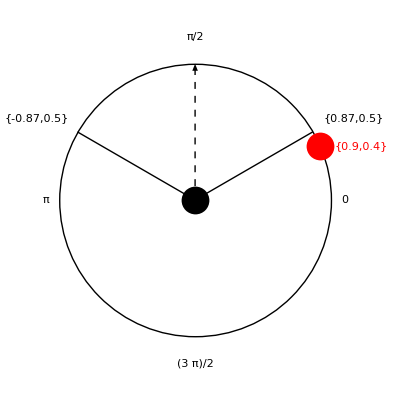

```mathematica
direction=Pi/2
zombiePoint= {0,0}
playerPoint = {7,3}
hypotenuse = Sqrt[playerPoint[[1]]^2 + playerPoint[[2]]^2]
adjacent = playerPoint[[1]]
opposite = playerPoint[[2]]
unitCircle = Circle[{0,0},1]

Graphics[
{
PointSize[0.05],


Point[zombiePoint],
{Dashed,Arrow[{{0,0},{0,1}}]},
Line[{zombiePoint,{Cos[Pi / 3.0 + Pi / 2.0],Sin[Pi / 3.0 + Pi / 2.0]}}],
Line[{zombiePoint,{Cos[Pi / 2.0 - Pi / 3.0 ],Sin[Pi / 2.0 - Pi / 3.0]}}],
unitCircle,
Red,
Point[{adjacent / hypotenuse, opposite / hypotenuse}],
FontSize->12,
Text[{SetPrecision[adjacent / hypotenuse,2], SetPrecision[opposite / hypotenuse,2]}, {adjacent / hypotenuse+0.3, opposite / hypotenuse}],
Black,
Text[{SetPrecision[Cos[Pi / 3.0 + Pi / 2.0],2],SetPrecision[Sin[Pi / 3.0 + Pi / 2.0],2]},{Cos[Pi / 3.0 + Pi / 2.0]-0.3,Sin[Pi / 3.0 + Pi / 2.0]+0.1}],
Text[{SetPrecision[Cos[Pi / 2.0 - Pi / 3.0],2],SetPrecision[Sin[Pi / 2.0 - Pi / 3.0],2]},{Cos[Pi / 2.0 - Pi / 3.0]+0.3,Sin[Pi / 2.0 - Pi / 3.0]+0.1}],
Black,
FontSize->20,
Text[Pi/2,{ 0,1.2}],
Text["0", {1.1,0}],
Text[Pi, {-1.1,0}],
Text[3Pi/2,{0,-1.2}]
}
]

Graphics[
{
PointSize[0.05],
FontSize->20,
Text[zombiePoint, {zombiePoint[[1]],zombiePoint[[2]]+1.2}],
Point[zombiePoint], 
Red,
Text[playerPoint, {playerPoint[[1]],playerPoint[[2]]+1.2}],
Point[playerPoint]
}, 
Frame->{1,1},
PlotRange->{{-10,10},{-10,10}}
]

Graphics[
{
Line[{{-2Pi,0},{4Pi,0}}],
FontSize->20,
Text[-2Pi,{-2Pi-1,0}],
Text[4Pi,{4Pi+0.6,0}],
Red,
Text[SetPrecision[N[ArcCos[adjacent/hypotenuse]],2],{ArcCos[adjacent/hypotenuse],0-0.7}],
Black,
Text[SetPrecision[N[Pi / 3.0 + Pi / 2.0],2], {Pi / 3.0 + Pi / 2.0, 0 + 0.4}],
Text[SetPrecision[N[Pi / 2.0 - Pi / 3.0],2], {Pi / 2.0 - Pi / 3.0, 0 + 0.4}],
Arrow[{{0.52,1},{2.6,1}}],
Arrow[{{2.6,1},{0.52,1}}]
}
]
```

```mathematica
Export["step1trig.png",%1706,"PNG"]
```

step1trig.png

```mathematica
Export["step1trig",%1706,"PNG"]
```

step1trig

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["step1trig"]]]
```

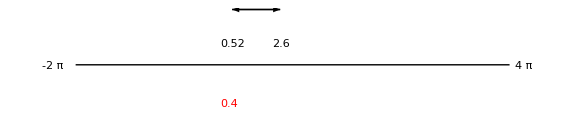

```mathematica
Show[%1708,ImageSize->Large]
```

```mathematica
Export["step3trig.png",%1727,"PNG"]
```

step3trig.png

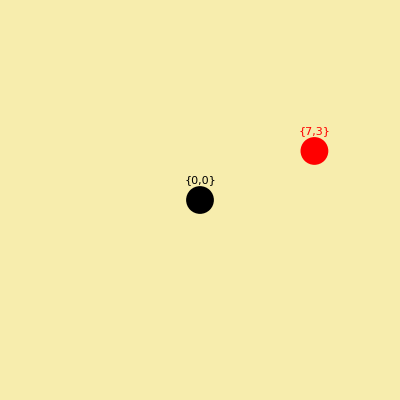

```mathematica
Show[Graphics[{PointSize[0.05],FontSize->20,Text[{0,0},{0,1.2}],Point[{0,0}],RGBColor[1,0,0],Text[{7,3},{7,4.2}],Point[{7,3}]},Frame->{1,1},PlotRange->{{-10,10},{-10,10}}],Background->RGBColor[0.97,0.93,0.68]]
```

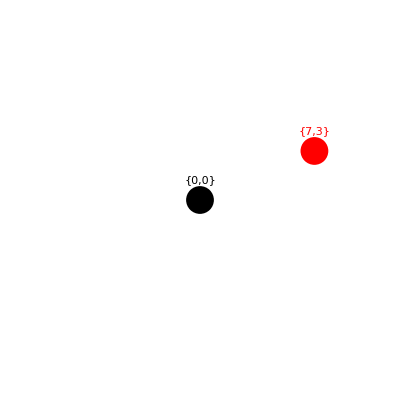

```mathematica
Show[%1709,Background->White]
```

```mathematica
Export["step1trig.png",%1732,"PNG"]
```

step1trig.png

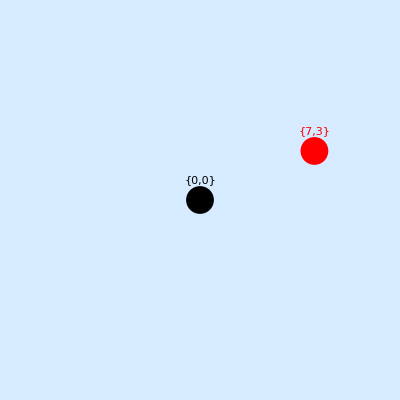

```mathematica
Show[Graphics[{PointSize[0.05],FontSize->20,Text[{0,0},{0,1.2}],Point[{0,0}],RGBColor[1,0,0],Text[{7,3},{7,4.2}],Point[{7,3}]},Frame->{1,1},PlotRange->{{-10,10},{-10,10}}],Background->RGBColor[0.84,0.92,1.]]
```

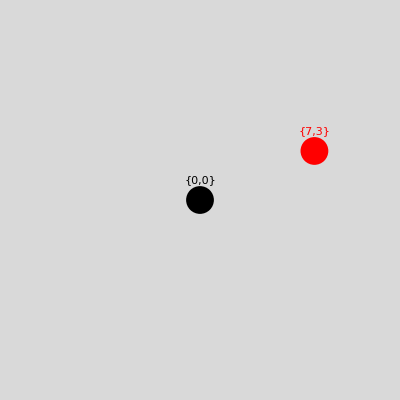

```mathematica
Show[Graphics[{PointSize[0.05],FontSize->20,Text[{0,0},{0,1.2}],Point[{0,0}],RGBColor[1,0,0],Text[{7,3},{7,4.2}],Point[{7,3}]},Frame->{1,1},PlotRange->{{-10,10},{-10,10}}],Background->LightGray]
```

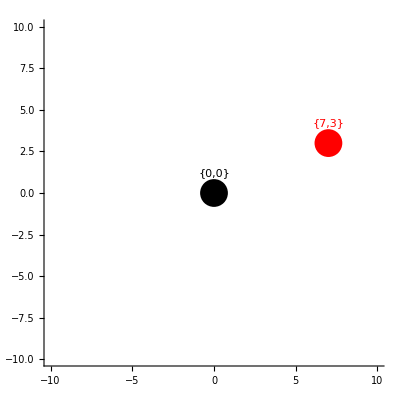

```mathematica
Show[Graphics[{PointSize[0.05],FontSize->20,Text[{0,0},{0,1.2}],Point[{0,0}],RGBColor[1,0,0],Text[{7,3},{7,4.2}],Point[{7,3}]},Frame->{1,1},PlotRange->{{-10,10},{-10,10}}],Axes->True,AxesStyle->Gray]
```

```mathematica
Show[%1694,Axes->False]
```

-Graphics-

```mathematica
Show[%1680,ImageSize->Large]
```

-Graphics-

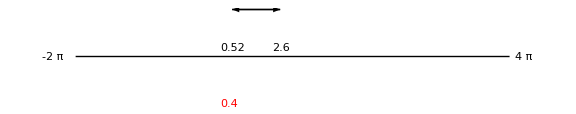

```mathematica
Show[%1658,ImageSize->Large]
```

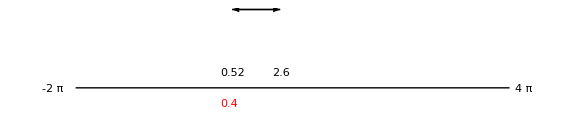

```mathematica
Show[%1637,ImageSize->Large]
```

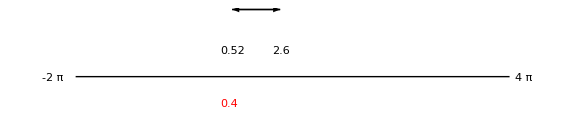

```mathematica
Show[%1617,ImageSize->Large]
```

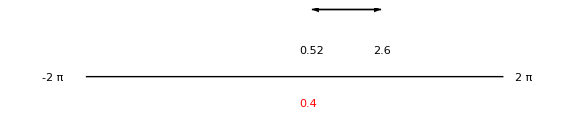

```mathematica
Show[%1579,ImageSize->Large]
```

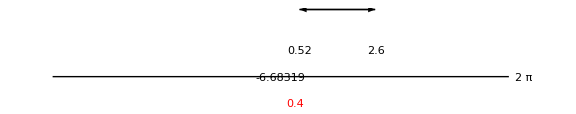

```mathematica
Show[%1525,ImageSize->Large]
```

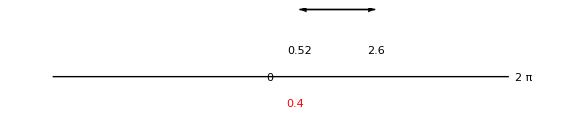

```mathematica
Show[%1474,ImageSize->Large]
```

```mathematica
Show[Graphics[{PointSize[0.05],FontSize->20,Text[{0,0},{0,1.2}],Point[{0,0}],RGBColor[1,0,0],Text[{7,3},{7,4.2}],Point[{7,3}]},Frame->{1,1},PlotRange->{{-10,10},{-10,10}}],Axes->True,AxesStyle->Gray]
```

-Graphics-

```mathematica
Show[%1442,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.]],Method->{"AxesInFront"->False}]
```

-Graphics-

```mathematica
Show[%1443,Background->None]
```

-Graphics-

```mathematica
Show[%1443,Background->None]
```

-Graphics-

```mathematica
Show[%1443,Axes->False]
```

-Graphics-

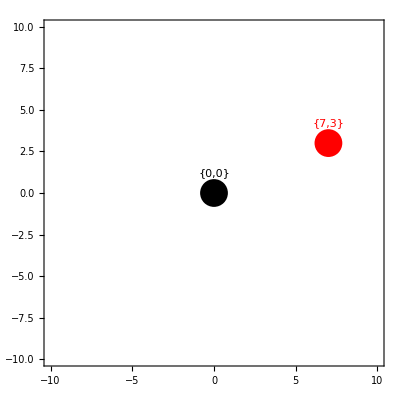

```mathematica
Show[Graphics[{PointSize[0.05],FontSize->20,Text[{0,0},{0,1.2}],Point[{0,0}],RGBColor[1,0,0],Text[{7,3},{7,4.2}],Point[{7,3}]},Frame->{1,1},PlotRange->{{-10,10},{-10,10}}],Frame->True,FrameStyle->Black]
```